# Synthesizing invariant barrier certificates

This prototypical implementation is dedicated to synthesizing invariant barrier certificates via difference-of-convex programming. It takes as input a differential dynamical system together with an initial and an unsafe set, and tries to find an invariant barrier certificate B(x) (in the form of a given template) that suffices to prove unbounded-time safety of the system.

Current version: v1.0
Validated on platform: Wolfram Mathematica 12.1.0.0, 64 bit-CentOS Linux-7.8.2003
Latest modification: on April 28, 2021, by Mingshuai Chen, RWTH Aachen

Corresponding e-mail: chenms@cs.rwth-aachen.de
List of contributors: Mingshuai Chen, Qiuye Wang, Bai Xue, Naijun Zhan, Joost-Pieter Katoen

Comments and bug-reports are highly appreciated.
© 2021 Lehrstuhl für Informatik 2, RWTH Aachen University. MIT Licensed.

## Source code

```mathematica
Clear["Global`*"];
```

```mathematica
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

```mathematica
main[varSet_,flowVec_,domainRange_,initialBoundary_,unsafeBoundary_,barrierDegree_,polyDegrees_,paraRange_,LieOrder_,ϵI_,ϵU_,ϵL_,ϵ_,δ_,bilinearUnsafeCons_,posteriorCheck_,verbose_,bcTempDefault_:Automatic]:=Module[{time,SDPTime,SDPTimeInitial,sysDim,bcTemp,rank,LieSequence,LieConstraints,sosSet,sosConstraint,parameters,cMatrix,cMatrixSet,coff,bcCoff,polyCoff,SDPVars,matC,matH,matG,matF,matGamma,matOmegaH,matOmegaG,matM,matI,matKronecker,eigenValues,eigenVectors,matV,matD,matDPlus,matDMinus,matM1,matM2,matN,BMI2,dBMI2,BMI2Rules,LMISet,LMIConstraint,matCorner,matCornerUT1,matCornerUT2,paraRegion,zCoff,zkCoff,zaLambda,bcLambda,matNzI,matLinear,σI,σU,basis,degree,optimumSequence,optimum,point,maximum,initialVector,initialRules,initialSDPVars,bcCandidate,solutionDist,verifiedInitial,verifiedUnsafe,verifiedLie,QECheckLie,i,j,k,n},
time=TimeUsed[];

sysDim=Length[varSet];

(*set up BC template*)
If[bcTempDefault===Automatic,bcTemp=polyTemp[varSet,a,barrierDegree],bcTemp=bcTempDefault];
Print["Template BC: \n",bcTemp];

If[LieOrder>1,
(*compute the rank Subscript[N, B,f]*)
i=1;
While[True,
LieSequence=LieDerivatives[varSet,flowVec,bcTemp,i+1];
If[PolynomialReduce[LieSequence[[-1]],GroebnerBasis[Drop[LieSequence,-1],Variables[LieSequence]],Variables[LieSequence]][[-1]]==0,rank=i;Break[]];
i++;
](*;
Print["N_(B,f)=",rank];*)
];

(*generate the sequence of Lie derivatives*)
LieSequence=LieDerivatives[varSet,flowVec,bcTemp,LieOrder];
Print["Lie sequence: \n",LieSequence];

(*encode sufficient BC conditions*)
sosSet={};
σI=polyTemp[varSet,w,polyDegrees[[1]]];
σU=polyTemp[varSet,u,polyDegrees[[2]]];
sosSet=If[bilinearUnsafeCons,{σI,σU,-bcTemp+σI*initialBoundary-ϵI,unsafeBoundary+σU*bcTemp-ϵU},{σI,σU,-bcTemp+σI*initialBoundary-ϵI,bcTemp+σU*unsafeBoundary-ϵU}];
LieConstraints=Table[-LieSequence[[i+1]]+Sum[polyTemp[varSet,identifier[{v,i,j}],polyDegrees[[3]]]*LieSequence[[j+1]],{j,0,i-1}]-ϵL,{i,1,LieOrder}];
sosSet=Map[Collect[#,varSet,Simplify]&,Join[sosSet,LieConstraints]];
Print["SOS constraints:\n",sosSet];

(*decompose to LMI constraints*)
Print["Decomposing to LMI constraints",If[!verbose," (dislay suppressed)",""]," ..."];
cMatrixSet={};
LMISet={};
For[n=1,n≤Length[sosSet],n++,
sosConstraint=sosSet[[n]];
(*parameters=Complement[Variables[sosConstraint],varSet];*)

(*extract coefficient matrix*)
degree=Ceiling[polyDegree[sosConstraint,varSet]/2];
(*degree=Which[n≤2,Ceiling[polyDegrees[[n]]/2],n≤4,sosDegrees[[n-2]],n>4,sosDegrees[[-1]]];*)
basis=monomList[varSet,degree];
cMatrix=coefficientMatrix[varSet,basis,sosConstraint];
If[verbose,Print["For the ",Switch[n,1,"σ^ℐ",2,"σ^𝒰",3,"initial",4,"unsafe",_,"Lie"], " constraint with basis=",basis," of degree=",polyDegree[sosConstraint,varSet],":\nF(a,s)=",-cMatrix//MatrixForm]];
cMatrix=-cMatrix+λ*IdentityMatrix[Length[cMatrix]];
AppendTo[cMatrixSet,cMatrix];

(*If[n==3,
zaLambda=Table[Subscript[z, i],{i,1,Length[parameters]+1}];
SDPVars=Append[parameters,λ];
BMI2Rules=Thread[SDPVars->zaLambda]
];
If[polyDegree[sosConstraint,parameters]≤1,AppendTo[LMISet,cMatrix];Continue[]];*)
If[n≤2,AppendTo[LMISet,cMatrix];Continue[]];

(*matrix polynomial form*)
coff=Variables[cMatrix];
bcCoff=Cases[coff,Subscript[a,_]];
polyCoff=Complement[coff,bcCoff];
matC=cMatrix/.Thread[coff->0];
matH=Table[Coefficient[cMatrix/.Thread[Cases[coff,Except[bcCoff[[i]]]]->0],bcCoff[[i]]],{i,1,Length[bcCoff]}];
matG=Table[Coefficient[cMatrix/.Thread[Cases[coff,Except[polyCoff[[i]]]]->0],polyCoff[[i]]],{i,1,Length[polyCoff]}];
matF=Table[Coefficient[cMatrix,bcCoff[[i]]*polyCoff[[j]]],{i,1,Length[bcCoff]},{j,1,Length[polyCoff]}];
(*Print["Matrix polynomial form:"];
Print["B(λ,a,s)=",MatrixForm[matC]+Sum[bcCoff[[i]]*MatrixForm[matH[[i]]],{i,1,Length[bcCoff]}]+Sum[polyCoff[[j]]*MatrixForm[matG[[j]]],{j,1,Length[polyCoff]}]+Sum[bcCoff[[i]]*polyCoff[[j]]*MatrixForm[matF[[i]][[j]]],{i,1,Length[bcCoff]},{j,1,Length[polyCoff]}]];*)

(*intermediate matrices*)
matOmegaH=Join[Sequence@@Table[matH[[i]],{i,1,Length[bcCoff]}],2];
matOmegaG=Join[Sequence@@Table[matG[[j]],{j,1,Length[polyCoff]}],2];
matGamma=1/2Join[Sequence@@Table[Join[Sequence@@Table[matF[[i]][[j]],{j,1,Length[polyCoff]}],2],{i,1,Length[bcCoff]}]];
matM=SparseArray[{Band[{1,Dimensions[matGamma][[1]]+1}]->matGamma,Band[{Dimensions[matGamma][[1]]+1,1}]->Transpose[matGamma]},Plus@@Dimensions[matGamma]{1,1}];
(*Print["Ω_H=",matOmegaH//MatrixForm];
Print["Ω_G=",matOmegaG//MatrixForm];
Print["Γ=",matGamma//MatrixForm];
Print["M=",matM//MatrixForm];*)

(*matrix bilinear form*)
matI=IdentityMatrix[Length[basis]];
matKronecker=Join[KroneckerProduct[bcCoff,matI],KroneckerProduct[polyCoff,matI]];
(*Print["Matrix bilinear form:"];
Print["B_M(λ,a,s)=",MatrixForm[Transpose[matKronecker]],".",MatrixForm[matM],".",MatrixForm[matKronecker],"+",MatrixForm[Join[matOmegaH,matOmegaG,2]],".",MatrixForm[matKronecker],"+",MatrixForm[matC]];*)
If[verbose,Print["B_M(λ,a,s)=",Transpose[matKronecker].matM.matKronecker+Join[matOmegaH,matOmegaG,2].matKronecker+matC//MatrixForm]];

(*difference-of-convex decomposition*)
{eigenValues,eigenVectors}=Eigensystem[matM//Normal];
matD=DiagonalMatrix[eigenValues];
matV=Normalize/@eigenVectors;
matDPlus=Replace[matD,_?Negative->0,{-1}];
matDMinus=matDPlus-matD;
matM1=Chop[Transpose[matV].matDPlus.matV];
matM2=Chop[Transpose[matV].matDMinus.matV];
(*Print[matM==Chop[matM1-matM2]];*)
BMI2=Transpose[matKronecker].matM2.matKronecker;
(*Print["Decomposed matrix bilinear form:"];
Print["B_M^+(λ,a,s)=",MatrixForm[Transpose[matKronecker]],".",MatrixForm[matM1],".",MatrixForm[matKronecker],"+",MatrixForm[Join[matOmegaH,matOmegaG,2]],".",MatrixForm[matKronecker],"+",MatrixForm[matC]];
Print["B_M^-(λ,a,s)=",MatrixForm[Transpose[matKronecker]],".",MatrixForm[matM2],".",MatrixForm[matKronecker]];*)
If[verbose,Print["B_M^+(λ,a,s)=",Transpose[matKronecker].matM1.matKronecker+Join[matOmegaH,matOmegaG,2].matKronecker+matC//MatrixForm]];
If[verbose,Print["B_M^-(λ,a,s)=",Transpose[matKronecker].matM2.matKronecker//MatrixForm]];

(*LMI constraint*)
matN=Chop[Transpose[matV].MatrixPower[matDPlus,1/2].matV];
(*Print[Chop[matNᵀ.matN-matM1]];*)
zCoff=Join[bcCoff,polyCoff];
matKronecker=KroneckerProduct[zCoff,matI];
matNzI=matN.matKronecker;
(*Print["matNzI=",matN//MatrixForm,".",matKronecker//MatrixForm];
Print["matNzI=",matNzI//MatrixForm];*)
matLinear=Join[matOmegaH,matOmegaG,2].matKronecker+matC;
(*Print["matLinear=",matLinear//MatrixForm];*)
bcLambda=Append[bcCoff,λ];
If[n==3,
zaLambda=Table[Subscript[z, i],{i,1,Length[bcCoff]+1}];
SDPVars=bcLambda;
BMI2Rules=Thread[SDPVars->zaLambda]
];
zkCoff=Table[Subscript[z, i],{i,Length[SDPVars]+1,Length[SDPVars]+Length[polyCoff]-1}];
BMI2Rules=DeleteDuplicates[Join[BMI2Rules,Thread[DeleteCases[polyCoff,λ]->zkCoff]]];
zkCoff=Join[zaLambda,zkCoff];
(*Print["Rules for evaluating B_M_2(z):\n",BMI2Rules];*)
(*dBMI2=(zCoff-(zCoff/.BMI2Rules)).((D[BMI2,#]&/@zCoff)/.BMI2Rules);*)
dBMI2=(zCoff-zkCoff).((D[BMI2,#]&/@zCoff)/.BMI2Rules);
(*Print["(zCoff-zkCoff)=",zCoff-zkCoff];
Print["((D[BMI2,#]&/@zCoff)/.BMI2Rules)=",((D[BMI2,#]&/@zCoff)/.BMI2Rules)];
Print["dBMI2=",dBMI2];*)
(*dBMI2=Sum[(zCoff-zkCoff)[[i]]*((D[BMI2,#]&/@zCoff)/.BMI2Rules)[[i]],{i,1,Length[zCoff]}];*)
(*Print["dBMI2=",dBMI2//MatrixForm];*)
(*make matCorner symmetric (otherwise asymmetric due to numerical errors)*)
matCorner=matLinear-(BMI2/.BMI2Rules)-dBMI2;
matCornerUT1=UpperTriangularize[matCorner];
matCornerUT2=UpperTriangularize[matCorner,1];
matCorner=matCornerUT1+Transpose[matCornerUT2];
LMIConstraint=Join[Join[-IdentityMatrix[Length[zCoff]*Length[basis]],matNzI,2],Join[Transpose[matNzI],matCorner,2]];
(*Print["LMIConstraint:\n",LMIConstraint//MatrixForm];*)
(*LMIConstraint=SparseArray[LMIConstraint];*)
AppendTo[LMISet,LMIConstraint];
SDPVars=DeleteDuplicates[Join[SDPVars,zCoff]];
];

Print["LMI constraints:\n",SparseArray/@LMISet];
Print["LMI variables:\n",SDPVars];
Print["Variable correspondence:\n",BMI2Rules];
(*Print["cMatrix set:\n",MatrixForm/@cMatrixSet];*)

(*solve a series of LMI constraints*)
optimumSequence={};

(*find an initial feasible solution*)
(*initialVector=Replace[SDPVars,{Subscript[x_, y_]/;StringMatchQ[ToString[x],RegularExpression["v.*"]]&&StringMatchQ[ToString[y],RegularExpression["00+"]]->RandomReal[-paraRange,WorkingPrecision->2],Subscript[x_, y_]/;x=!=a&&StringMatchQ[ToString[y],RegularExpression["00+"]]->RandomReal[paraRange,WorkingPrecision->2],Subscript[x_,_]/;StringMatchQ[ToString[x],RegularExpression["[wuv].*"]]->0},{1}];*)
initialVector=Replace[SDPVars,{Subscript[x_, y_]/;StringMatchQ[ToString[x],RegularExpression["v.*"]]&&StringMatchQ[ToString[y],RegularExpression["00+"]]->-1,Subscript[x_, y_]/;x=!=a&&StringMatchQ[ToString[y],RegularExpression["00+"]]->1,Subscript[x_,_]/;StringMatchQ[ToString[x],RegularExpression["[wuv].*"]]->0},{1}];
Print["Initial vector:\n",initialVector];
initialRules=Thread[SDPVars->initialVector];
initialSDPVars=DeleteCases[initialVector,_?NumericQ];
paraRegion=Cuboid[Table[paraRange[[1]],Length[initialSDPVars]-1],Table[paraRange[[2]],Length[initialSDPVars]-1]];
SDPTimeInitial=TimeUsed[];
{point,maximum}=SemidefiniteOptimization[-λ,{Table[(cMatrixSet/.initialRules)[[i]](\[VectorLessEqual])_(Dimensions[cMatrixSet[[i]]][[1]])0,{i,1,Length[cMatrixSet]}],DeleteCases[initialSDPVars,λ]∈paraRegion},initialSDPVars,{"PrimalMinimizerRules","PrimalMinimumValue"},PerformanceGoal->"Quality"];
SDPTimeInitial=TimeUsed[]-SDPTimeInitial;
maximum=-maximum;
optimum=Thread[(SDPVars/.BMI2Rules)->(initialVector/.point)];
Print["Initial feasible solution:\nz^0=",Map[#/.#/;#[[1]]===(λ/.BMI2Rules):>Style[#,Bold]&,optimum]];
Print["Initial maximum:\nλ^0=",maximum];
AppendTo[optimumSequence,optimum];

(*encode quadratic objective as an extra constraint*)
LMIConstraint=-Join[{Prepend[SDPVars-(SDPVars/.BMI2Rules),2ζ/δ]},Join[List/@(SDPVars-(SDPVars/.BMI2Rules)),IdentityMatrix[Length[SDPVars]],2]];
(*Print["LMIConstraint=",LMIConstraint//MatrixForm];*)
LMIConstraint=(LMIConstraint/.optimum)(\[VectorLessEqual])_(Dimensions[LMIConstraint][[1]])0;
AppendTo[SDPVars,ζ];
AppendTo[BMI2Rules,ζ->zz];
(*AppendTo[optimum,zz->0];*)
Print["LMI variables:\n",SDPVars];
Print["Variable correspondence:\n",BMI2Rules];

(*solve LMI constraints in sequence*)
(*Print["Semidefinite optimization starts-------"];*)
k=1;
SDPTime=TimeUsed[];
While[((λ/.BMI2Rules)/.optimum)<-10^-5&&k≤100,
(*quadratic term currently not supported by the SDP solver in mathematica, use λ only*)
(*If[k==27||k==26||k==1,
For[i=1,i≤Length[LMISet],i++,
Print[(LMISet/.optimum)[[i]]];
Print["Symmetric: ",SymmetricMatrixQ[(LMISet/.optimum)[[i]]],"Hermitian: ",HermitianMatrixQ[(LMISet/.optimum)[[i]]]];
];
];*)
paraRegion=Cuboid[Table[paraRange[[1]],Length[SDPVars]],Table[paraRange[[2]],Length[SDPVars]]];
{point,maximum}=SemidefiniteOptimization[-λ-ζ,{Append[Table[(LMISet/.optimum)[[i]](\[VectorLessEqual])_(Dimensions[LMISet[[i]]][[1]])0,{i,1,Length[LMISet]}],LMIConstraint],SDPVars∈paraRegion},SDPVars,{"PrimalMinimizerRules","PrimalMinimumValue"},PerformanceGoal->"Quality"];
maximum=-maximum;
optimum=Thread[(SDPVars/.BMI2Rules)->(SDPVars/.point)];
(*Print["Feasible solution:\n",Superscript["z",k],"=",Map[#/.#/;#[[1]]===(λ/.BMI2Rules):>Style[#,Bold]&,optimum]];*)
(*Print["Maximum:\n",Superscript["(λ+ζ)",k],"=",maximum];*)
AppendTo[optimumSequence,optimum];
solutionDist=Norm[Drop[((SDPVars/.BMI2Rules)/.(optimumSequence[[-1]]))-((SDPVars/.BMI2Rules)/.(optimumSequence[[-2]])),-1]];
(*Print["|",Superscript["z",k],"-",Superscript["z",k-1],"|=",solutionDist];*)
(*solutionDist=(2(ζ/.BMI2Rules)/.optimum)/δ;
Print["z","-","z","≤",solutionDist];*)
If[solutionDist≤ϵ,
Print["Close enough solutions: ",solutionDist," ≤ ϵ = ",ϵ];k++;
Break[]];
k++;
];
SDPTime=TimeUsed[]-SDPTime+SDPTimeInitial;
(*Print["Semidefinite optimization terminates-------"];*)

If[k>100,Print["Maximum no. of iterations (100) reached."]];

(*If[((λ/.BMI2Rules)/.optimum)≥-10^-5,*)
bcCandidate=(bcTemp/.BMI2Rules)/.optimum;
If[LieOrder>1,
bcCandidate=bcCandidate/.x_/;Abs[x]≤10^-5->0;
LieSequence=LieDerivatives[varSet,flowVec,bcCandidate,LieOrder];
];
Print["Barrier certificate candidate:\n",bcCandidate];

(*post verification due to numerical issues*)
If[posteriorCheck,
Off[Reduce::ratnz,General::notfound,General::infy,General::indet,ReplaceAll::reps];

Print["Post verification due to numerical issues:"];
verifiedInitial=Reduce[ForAll[varSet,initialBoundary≤0⇒bcCandidate≤0],Reals];
Print["∀x. ℐ(x)≤0 ⇒ B(x)≤0: ",verifiedInitial];
verifiedUnsafe=Reduce[ForAll[varSet,bcCandidate≤0⇒unsafeBoundary>0],Reals];
Print["∀x. B(x)≤0 ⇒ 𝒰(x)>0: ",verifiedUnsafe];
If[LieOrder>1,
QECheckLie=If[LieOrder<rank,ForAll[varSet,And@@Table[domainRange[[1]]≤varSet[[j]]≤domainRange[[2]],{j,1,Length[varSet]}]⇒And@@Append[Table[(And@@Thread[((Drop[LieSequence,{i,Length[LieSequence]}]/.BMI2Rules)/.optimum)==0])⇒((LieSequence[[i]]/.BMI2Rules)/.optimum)≤0,{i,2,Length[LieSequence]-1}],(And@@Thread[((Drop[LieSequence,-1]/.BMI2Rules)/.optimum)==0])⇒((LieSequence[[-1]]/.BMI2Rules)/.optimum)<0]],ForAll[varSet,And@@Table[domainRange[[1]]≤varSet[[j]]≤domainRange[[2]],{j,1,Length[varSet]}]⇒And@@Table[(And@@Thread[((Drop[LieSequence,{i,Length[LieSequence]}]/.BMI2Rules)/.optimum)==0])⇒((LieSequence[[i]]/.BMI2Rules)/.optimum)≤0,{i,2,Length[LieSequence]}]]],
QECheckLie=ForAll[varSet,And@@Table[domainRange[[1]]≤varSet[[j]]≤domainRange[[2]],{j,1,Length[varSet]}]⇒And@@Table[(And@@Thread[((Drop[LieSequence,{i,Length[LieSequence]}]/.BMI2Rules)/.optimum)==0])⇒((LieSequence[[i]]/.BMI2Rules)/.optimum)≤0,{i,2,Length[LieSequence]}]]
];
verifiedLie=Reduce[QECheckLie,Reals];
Print["Lie consecution: ",verifiedLie];
];
(*render graphics*)
If[Length[varSet]==2,
Print["Graphical illustration:"];
renderGraphics2D[varSet,flowVec,bcCandidate,domainRange,initialBoundary,unsafeBoundary],
If[Length[varSet]==3,
Print["Graphical illustration:"];
renderGraphics3D[varSet,flowVec,bcCandidate,domainRange,initialBoundary,unsafeBoundary]
];
];
(*];*)

time=TimeUsed[]-time;
Print["SDP CPU-time elapsed: ",SDPTime,"s"];
Print["Total CPU-time elapsed: ",time,"s"];
Return[];
]

identifier[symbols_]:=ToExpression[StringJoin[ToString/@symbols]]

polyDegree[poly_,vars_]:=Module[{t},
Return[Exponent[poly/.Thread[vars->t*vars],t]];
];

polyTemp[vars_,a_,order_]:=Module[{n=Length@vars,idx,z},idx=Cases[Tuples[Range[0,order],n],x_/;Plus@@x≤order];
z=Times@@@(vars^#&/@idx);
z.((Subscript[a,Row[#]])&/@idx)
]

monomList=Function[{vars,degree},With[{explist=Flatten[Permutations/@PadRight[#,{Length@#,Length[vars]}]&[Flatten[IntegerPartitions[#,Length[vars]]&/@Range[0,degree],1]],1]//Transpose},Times@@@Transpose[vars^explist]]
];

LieDerivatives[vars_,flow_,bc_,order_]:=Module[{Lie,LieSequence,gradient,k},
Lie=bc;
LieSequence={Lie};
For[k=1,k≤order,k++,
gradient=Grad[Lie,vars];
Lie=Collect[gradient.flow,vars,Simplify];
AppendTo[LieSequence,Lie];
];
Return[LieSequence];
]

(*inefficient, to be re-written*)
coefficientMatrix[vars_,basis_,poly_]:=Module[{sym,i,j,A},
A=Table[sym[Min[i,j],Max[i,j]],{i,0,Length[basis]-1},{j,0,Length[basis]-1}];
(*Print[A//MatrixForm];
Print[poly];
Print[Solve[Not@Eliminate[Not[basis.A.basis==poly],vars],Flatten[A]][[1]]];*)
(*A=A/.Append[SolveAlways[basis.A.basis==poly,vars][[1]],sym[0,0]->(poly/.Thread[vars->0])];*)
Off[Solve::svars];
A=A/.Solve[Not@Eliminate[Not[basis.A.basis==poly],vars],Flatten[A]][[1]];
A=A/.sym[_,_]:>0;
Return[A];
]

(*coefficientMatrix[vars_,basis_,poly_]:=Module[{i,j,position},
Print[poly,"\n",polyDegree[poly,vars]];
position=Table[sym[i],{i,1,Binomial[Length[vars]+polyDegree[poly,vars],Length[vars]]}];
Print[position];
(*For[i=1,i≤Length[basis],i++,
For[j=1,j≤Length[basis],j++,
basis[[i]]*basis[[j]]
]
];*)
]*)

renderGraphics2D[varSet_,flowVec_,bc_,domainRange_,initialBoundary_,unsafeBoundary_]:=Module[{graphics,initialSamples,traj,trajPlot,flowPlot,bcPlot,initialPlot,unsafePlot,ranges,i},
ranges=Table[Prepend[domainRange,varSet[[i]]],{i,1,Length[varSet]}];
ranges=Sequence@@ranges;
initialSamples=RandomPoint[ImplicitRegion[initialBoundary≤0,varSet],20];
Off[NDSolve::ndsz];
traj[x0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==x0]],varSet,{t,0,20},Method->"StiffnessSwitching"];
trajPlot=ParametricPlot[Evaluate[(#[t]&/@varSet)/.traj[#]&/@initialSamples],{t,0,20},RegionFunction->((domainRange[[1]]≤#1≤domainRange[[2]])&&(domainRange[[1]]≤#2≤domainRange[[2]])&),PlotStyle->Directive[Black,Thickness[Medium]]](*/.Line[x_]:>Arrow[x]*);
(*trajPlot=StreamPlot[flowVec,Evaluate[ranges],StreamPoints->{Table[{initialSamples[[i]],Blue},{i,Length[initialSamples]}],Automatic,10^50},Epilog->Point[initialSamples]];*)
flowPlot=VectorPlot[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];
initialPlot=RegionPlot[initialBoundary≤0,Evaluate[ranges],PlotStyle->Directive[Blue],PlotLegends->SwatchLegend[{"ℐ(x) ≤ 0"}]];
unsafePlot=RegionPlot[unsafeBoundary≤0,Evaluate[ranges],PlotStyle->Directive[Red],PlotLegends->SwatchLegend[{"𝒰(x) ≤ 0"}]];
bcPlot=RegionPlot[bc≤0,Evaluate[ranges],BoundaryStyle->{Dashed},PlotStyle->Directive[Opacity[.6],LightPink],PlotLegends->SwatchLegend[{"B(x) ≤ 0"}]];
graphics=Show[flowPlot,initialPlot,unsafePlot,bcPlot,trajPlot,Frame->True,FrameLabel->varSet,RotateLabel->False];
Print[graphics];
]

renderGraphics3D[varSet_,flowVec_,bc_,domainRange_,initialBoundary_,unsafeBoundary_]:=Module[{graphics,initialSamples,traj,trajPlot,flowPlot,bcPlot,initialPlot,unsafePlot,ranges,i},
ranges=Table[Prepend[domainRange,varSet[[i]]],{i,1,Length[varSet]}];
ranges=Sequence@@ranges;
initialSamples=RandomPoint[ImplicitRegion[initialBoundary≤0,varSet],3];
Off[NDSolve::ndsz];
traj[x0_]:=NDSolve[Join[Thread[#'[t]&/@varSet==(flowVec/.Table[varSet[[i]]->varSet[[i]][t],{i,1,Length[varSet]}])],Thread[#[0]&/@varSet==x0]],varSet,{t,0,20},Method->"StiffnessSwitching"];
trajPlot=ParametricPlot3D[Evaluate[(#[t]&/@varSet)/.traj[#]&/@initialSamples],{t,0,20},RegionFunction->((domainRange[[1]]≤#1≤domainRange[[2]])&&(domainRange[[1]]≤#2≤domainRange[[2]])&&(domainRange[[1]]≤#3≤domainRange[[2]])&),PlotStyle->Black](*/.Line[x_]:>Arrow[x]*);
(*trajPlot=StreamPlot[flowVec,Evaluate[ranges],StreamPoints->{Table[{initialSamples[[i]],Blue},{i,Length[initialSamples]}],Automatic,10^50},Epilog->Point[initialSamples]];*)
(*flowPlot=VectorPlot3D[flowVec,Evaluate[ranges],VectorScaling->Automatic,VectorSizes->Automatic,VectorColorFunction->None,VectorStyle->Gray];*)
initialPlot=RegionPlot3D[initialBoundary≤0,Evaluate[ranges],PlotStyle->Directive[Blue],PlotLegends->SwatchLegend[{"ℐ(x) ≤ 0"}]];
unsafePlot=RegionPlot3D[unsafeBoundary≤0,Evaluate[ranges],PlotStyle->Directive[Red],PlotLegends->SwatchLegend[{"𝒰(x) ≤ 0"}]];
bcPlot=RegionPlot3D[bc≤0,Evaluate[ranges],PlotStyle->Directive[Opacity[.2],Pink],MeshStyle->Opacity[0.4],PlotLegends->SwatchLegend[{"B(x) ≤ 0"}]];
graphics=Show[initialPlot,unsafePlot,bcPlot,trajPlot,Frame->True,FrameLabel->varSet,RotateLabel->False];
Print[graphics];
(*Print[Show[flowPlot,initialPlot,unsafePlot,bcPlot,trajPlot,Frame->True,FrameLabel->varSet,RotateLabel->False]]*)
]
```

## Examples

```mathematica
varSet1={Subscript[x, 1],Subscript[x, 2]};
flowVec1={Subscript[x, 1],Subscript[x, 2]};
domainRange1={0,2};
initialBoundary1=(Subscript[x, 1]-1.125)^2+(Subscript[x, 2]-0.625)^2-0.0125;
unsafeBoundary1=(Subscript[x, 1]-0.875)^2+(Subscript[x, 2]-0.125)^2-0.0125;
barrierDegree1=2;
polyDegrees1={2,2,0};
paraRange1={-10,10};
LieOrder1=1;
ϵI1=ϵL1=0;
ϵU1=N[10^-2];
ϵ1=N[10^-3];
δ1=-N[10^-3];
bilinearUnsafeCons1=False;
posteriorCheck1=True;
verbose1=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,2 a_20 x_1^2+a_01 x_2+2 a_02 x_2^2+x_1 (a_10+2 a_11 x_2)}

SOS constraints:
{w_00+w_20 x_1^2+w_01 x_2+w_02 x_2^2+x_1 (w_10+w_11 x_2),u_00+u_20 x_1^2+u_01 x_2+u_02 x_2^2+x_1 (u_10+u_11 x_2),-a_00+1.64375 w_00+w_20 x_1^4+(-a_01-1.25 w_00+1.64375 w_01) x_2+(-a_02+w_00-1.25 w_01+1.64375 w_02) x_2^2+(w_01-1.25 w_02) x_2^3+w_02 x_2^4+x_1^3 (w_10-2.25 w_20+w_11 x_2)+x_1^2 (-a_20+w_00-2.25 w_10+1.64375 w_20+(w_01-2.25 w_11-1.25 w_20) x_2+(w_02+w_20) x_2^2)+x_1 (-a_10-2.25 w_00+1.64375 w_10+(-a_11-2.25 w_01-1.25 w_10+1.64375 w_11) x_2+(-2.25 w_02+w_10-1.25 w_11) x_2^2+w_11 x_2^3),-0.01+a_00+0.76875 u_00+u_20 x_1^4+(a_01-0.25 u_00+0.76875 u_01) x_2+(a_02+u_00-0.25 u_01+0.76875 u_02) x_2^2+(u_01-0.25 u_02) x_2^3+u_02 x_2^4+x_1^3 (u_10-1.75 u_20+u_11 x_2)+x_1^2 (a_20+u_00-1.75 u_10+0.76875 u_20+(u_01-1.75 u_11-0.25 u_20) x_2+(u_02+u_20) x_2^2)+x_1 (a_10-1.75 u_00+0.76875 u_10+(a_11-1.75 u_01-0.25 u_10+0.76875 u_11) x_2+(-1.75 u_02+u_10-0.25 u_11) x_2^2+u_11 x_2^3),a_00 v10_00+a_20 (-2+v10_00) x_1^2+a_01 (-1+v10_00) x_2+a_02 (-2+v10_00) x_2^2+x_1 (a_10 (-1+v10_00)+a_11 (-2+v10_00) x_2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,w_01,w_02,w_10,w_11,w_20,u_00,u_01,u_02,u_10,u_11,u_20,v10_00}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,w_01→z_9,w_02→z_10,w_10→z_11,w_11→z_12,w_20→z_13,u_00→z_14,u_01→z_15,u_02→z_16,u_10→z_17,u_11→z_18,u_20→z_19,v10_00→z_20}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,0,0,0,0,0,1,0,0,0,0,0,-1}

Initial feasible solution:
z^0={z_1→0.00742217,z_2→-1.11111×10^-7,z_3→-0.63772,z_4→1.68006×10^-8,z_5→0.182913,z_6→-0.0105912,z_7→-0.00742216,z_8→1,z_9→0,z_10→0,z_11→0,z_12→0,z_13→0,z_14→1,z_15→0,z_16→0,z_17→0,z_18→0,z_19→0,z_20→-1}

Initial maximum:
λ^0=-0.00742216

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,w_01,w_02,w_10,w_11,w_20,u_00,u_01,u_02,u_10,u_11,u_20,v10_00,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,w_01→z_9,w_02→z_10,w_10→z_11,w_11→z_12,w_20→z_13,u_00→z_14,u_01→z_15,u_02→z_16,u_10→z_17,u_11→z_18,u_20→z_19,v10_00→z_20,ζ→zz}

Maximum no. of iterations (100) reached.

Barrier certificate candidate:
0.00470861+0.0000115575 x_1-0.000562259 x_1^2-0.0000785699 x_2+0.0209193 x_1 x_2-0.0701312 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

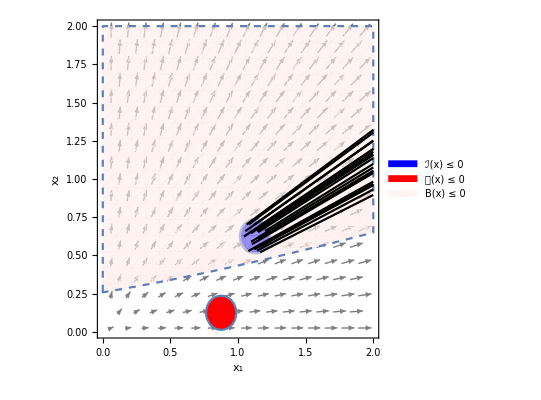

SDP CPU-time elapsed: 4.625s

Total CPU-time elapsed: 4.828s

```mathematica
main[varSet1,flowVec1,domainRange1,initialBoundary1,unsafeBoundary1,barrierDegree1,polyDegrees1,paraRange1,LieOrder1,ϵI1,ϵU1,ϵL1,ϵ1,δ1,bilinearUnsafeCons1,posteriorCheck1,verbose1];
```

```mathematica
varSet2={Subscript[x, 1],Subscript[x, 2]};
flowVec2={-2 Subscript[x, 2],Subscript[x, 1]^2};
domainRange2={-2,2};
initialBoundary2=(Subscript[x, 1]+1)^2+(Subscript[x, 2]-0.5)^2-0.16;
unsafeBoundary2=(Subscript[x, 1]+1)^2+(Subscript[x, 2]+0.5)^2-0.16;
barrierDegree2=1;
polyDegrees2={0,0,1};
paraRange2={-10,10};
LieOrder2=1;
ϵI2=ϵU2=ϵL2=N[10^-3];
ϵ2=N[10^-6];
δ2=-N[10^-3];
bilinearUnsafeCons2=False;
posteriorCheck2=True;
verbose2=False;
```

Template BC: 
a_00+a_10 x_1+a_01 x_2

Lie sequence: 
{a_00+a_10 x_1+a_01 x_2,a_01 x_1^2-2 a_10 x_2}

SOS constraints:
{w_00,u_00,-0.001-a_00+1.09 w_00+(-a_10+2 w_00) x_1+w_00 x_1^2+(-a_01-1. w_00) x_2+w_00 x_2^2,-0.001+a_00+1.09 u_00+(a_10+2 u_00) x_1+u_00 x_1^2+(a_01+1. u_00) x_2+u_00 x_2^2,-0.001+a_00 v10_00+(-a_01+a_10 v10_10) x_1^2+(2 a_10+a_01 v10_00+a_00 v10_01) x_2+a_01 v10_01 x_2^2+x_1 (a_10 v10_00+a_00 v10_10+(a_10 v10_01+a_01 v10_10) x_2)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,v10_00→z_7,v10_01→z_8,v10_10→z_9}

Initial vector:
{a_00,a_01,a_10,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-0.421691,z_2→-0.835563,z_3→-0.417781,z_4→2.64081×10^-8,z_5→1,z_6→1,z_7→-1,z_8→0,z_9→0}

Initial maximum:
λ^0=2.64081×10^-8

LMI variables:
{a_00,a_01,a_10,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_10→z_3,λ→z_4,w_00→z_5,u_00→z_6,v10_00→z_7,v10_01→z_8,v10_10→z_9,ζ→zz}

Barrier certificate candidate:
-0.421691-0.417781 x_1-0.835563 x_2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

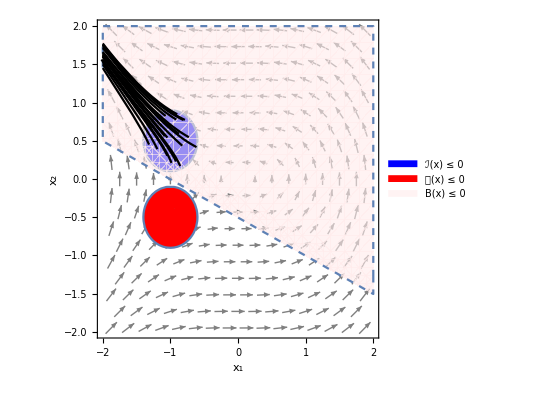

SDP CPU-time elapsed: 0.s

Total CPU-time elapsed: 0.219s

```mathematica
main[varSet2,flowVec2,domainRange2,initialBoundary2,unsafeBoundary2,barrierDegree2,polyDegrees2,paraRange2,LieOrder2,ϵI2,ϵU2,ϵL2,ϵ2,δ2,bilinearUnsafeCons2,posteriorCheck2,verbose2];
```

```mathematica
varSet6={Subscript[x, 1],Subscript[x, 2]};
flowVec6={-Subscript[x, 1]+ 2*Subscript[x, 1]^3*Subscript[x, 2]^2,-Subscript[x, 2]};
domainRange6={-2,2};
initialBoundary6=Subscript[x, 1]^2+(Subscript[x, 2]-0.5)^2-0.04;
unsafeBoundary6=(Subscript[x, 1]+1.5)^2+(Subscript[x, 2]+1.5)^2-0.25;
barrierDegree6=2;
polyDegrees6={0,0,1};
paraRange6={-10,10};
LieOrder6=1;
ϵI6=ϵU6=ϵL6=N[10^-3];
ϵ6=N[10^-6];
δ6=-N[10^-3];
bilinearUnsafeCons6=False;
posteriorCheck6=True;
verbose6=False;
```

Template BC: 
a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2

Lie sequence: 
{a_00+a_10 x_1+a_20 x_1^2+a_01 x_2+a_11 x_1 x_2+a_02 x_2^2,-2 a_20 x_1^2-a_01 x_2-2 a_02 x_2^2+4 a_20 x_1^4 x_2^2+x_1 (-a_10-2 a_11 x_2)+x_1^3 (2 a_10 x_2^2+2 a_11 x_2^3)}

SOS constraints:
{w_00,u_00,-0.001-a_00+0.21 w_00+(-a_20+w_00) x_1^2+(-a_01-1. w_00) x_2+(-a_02+w_00) x_2^2+x_1 (-a_10-a_11 x_2),-0.001+a_00+4.25 u_00+(a_20+u_00) x_1^2+(a_01+3. u_00) x_2+(a_02+u_00) x_2^2+x_1 (a_10+3. u_00+a_11 x_2),-0.001+a_00 v10_00+(a_01 (1+v10_00)+a_00 v10_01) x_2+(a_02 (2+v10_00)+a_01 v10_01) x_2^2-4 a_20 x_1^4 x_2^2+a_02 v10_01 x_2^3+x_1^2 (a_20 (2+v10_00)+a_10 v10_10+(a_20 v10_01+a_11 v10_10) x_2)+x_1 (a_10 (1+v10_00)+a_00 v10_10+(a_11 (2+v10_00)+a_10 v10_01+a_01 v10_10) x_2+(a_11 v10_01+a_02 v10_10) x_2^2)+x_1^3 (a_20 v10_10-2 a_10 x_2^2-2 a_11 x_2^3)}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12}

Initial vector:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,1,1,-1,0,0}

Initial feasible solution:
z^0={z_1→-1.1385,z_2→-1.68761,z_3→0.536489,z_4→-1.66584×10^-13,z_5→4.33857×10^-13,z_6→-2.17352×10^-10,z_7→1.30649×10^-8,z_8→1,z_9→1,z_10→-1,z_11→0,z_12→0}

Initial maximum:
λ^0=1.30649×10^-8

LMI variables:
{a_00,a_01,a_02,a_10,a_11,a_20,λ,w_00,u_00,v10_00,v10_01,v10_10,ζ}

Variable correspondence:
{a_00→z_1,a_01→z_2,a_02→z_3,a_10→z_4,a_11→z_5,a_20→z_6,λ→z_7,w_00→z_8,u_00→z_9,v10_00→z_10,v10_01→z_11,v10_10→z_12,ζ→zz}

Barrier certificate candidate:
-1.1385-1.66584×10^-13 x_1-2.17352×10^-10 x_1^2-1.68761 x_2+4.33857×10^-13 x_1 x_2+0.536489 x_2^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

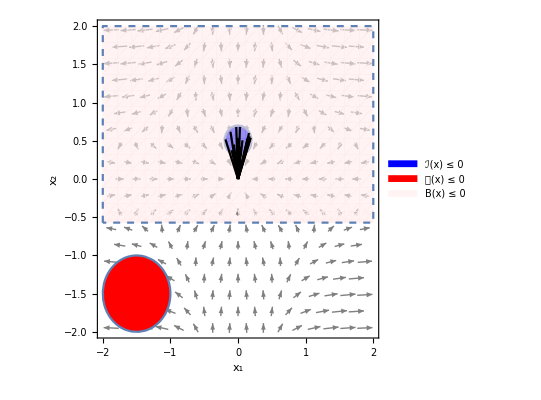

SDP CPU-time elapsed: 0.s

Total CPU-time elapsed: 0.141s

```mathematica
main[varSet6,flowVec6,domainRange6,initialBoundary6,unsafeBoundary6,barrierDegree6,polyDegrees6,paraRange6,LieOrder6,ϵI6,ϵU6,ϵL6,ϵ6,δ6,bilinearUnsafeCons6,posteriorCheck6,verbose6];
```

```mathematica
varSet7={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]};
flowVec7={10.0(-Subscript[x, 1]+Subscript[x, 2]),-Subscript[x, 2]+Subscript[x, 1] (28.0-Subscript[x, 3]),Subscript[x, 1] Subscript[x, 2]-(8 Subscript[x, 3])/3};
domainRange7={-20,20};
initialBoundary7=-0.25+(14.5+Subscript[x, 1])^2+(14.5+Subscript[x, 2])^2+(-12.5+Subscript[x, 3])^2;
unsafeBoundary7=-0.25+(16.5+Subscript[x, 1])^2+(14.5+Subscript[x, 2])^2+(-2.5+Subscript[x, 3])^2;
barrierDegree7=2;
polyDegrees7={0,0,1};
paraRange7={-1,1};
LieOrder7=1;
ϵI7=ϵU7=ϵL7=N[10^-3];
ϵ7=N[10^-6];
δ7=-N[10^-3];
bilinearUnsafeCons7=False;
posteriorCheck7=True;
verbose7=False;
```

```mathematica
main[varSet7,flowVec7,domainRange7,initialBoundary7,unsafeBoundary7,barrierDegree7,polyDegrees7,paraRange7,LieOrder7,ϵI7,ϵU7,ϵL7,ϵ7,δ7,bilinearUnsafeCons7,posteriorCheck7,verbose7];
```

Template BC: 
a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2

Lie sequence: 
{a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2,(-2 a_020+10. a_110) x_2^2-8/3 a_001 x_3-16/3 a_002 x_3^2+x_2 (-a_010+10. a_100-3.66667 (a_011-2.72727 a_101) x_3)+x_1^2 (28. a_110-20. a_200+a_101 x_2-a_110 x_3)+x_1 (28. a_010-10. a_100+a_011 x_2^2+(-a_010+28. a_011-12.6667 a_101) x_3-a_011 x_3^2+x_2 (a_001+56. a_020-11. a_110+20. a_200+2 (a_002-a_020) x_3))}

SOS constraints:
{w_000,u_000,-0.001-a_000+576.5 w_000+(-a_200+w_000) x_1^2+(-a_020+w_000) x_2^2+(-a_001-25. w_000) x_3+(-a_002+w_000) x_3^2+x_2 (-a_010+29. w_000-a_011 x_3)+x_1 (-a_100+29. w_000-a_110 x_2-a_101 x_3),-0.001+a_000+488.5 u_000+(a_200+u_000) x_1^2+(a_020+u_000) x_2^2+(a_001-5. u_000) x_3+(a_002+u_000) x_3^2+x_2 (a_010+29. u_000+a_011 x_3)+x_1 (a_100+33. u_000+a_110 x_2+a_101 x_3),-0.001+a_000 v10_000+a_200 v10_100 x_1^3+a_020 v10_010 x_2^3+(a_001 (8/3+v10_000)+a_000 v10_001) x_3+(a_002 (16/3+v10_000)+a_001 v10_001) x_3^2+a_002 v10_001 x_3^3+x_2^2 (-10. a_110+a_020 (2+v10_000)+a_010 v10_010+(a_020 v10_001+a_011 v10_010) x_3)+x_1^2 (-28. a_110+a_200 (20.+v10_000)+a_100 v10_100+(-a_101+a_200 v10_010+a_110 v10_100) x_2+(a_110+a_200 v10_001+a_101 v10_100) x_3)+x_2 (-10. a_100+a_010 (1+v10_000)+a_000 v10_010+(-10. a_101+a_011 (3.66667+v10_000)+a_010 v10_001+a_001 v10_010) x_3+(a_011 v10_001+a_002 v10_010) x_3^2)+x_1 (-28. a_010+a_100 (10.+v10_000)+a_000 v10_100+(-a_011+a_110 v10_010+a_020 v10_100) x_2^2+(a_010-28. a_011+12.6667 a_101+a_101 v10_000+a_100 v10_001+a_001 v10_100) x_3+(a_011+a_101 v10_001+a_002 v10_100) x_3^2+x_2 (-a_001-56. a_020+11. a_110-20. a_200+a_110 v10_000+a_100 v10_010+a_010 v10_100+(-2 a_002+2 a_020+a_110 v10_001+a_101 v10_010+a_011 v10_100) x_3))}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17}

Initial vector:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,1,1,-1,0,0,0}

Initial feasible solution:
z^0={z_1→-0.325894,z_2→-0.023822,z_3→0.000542765,z_4→0.00380387,z_5→-0.0000568394,z_6→0.000212731,z_7→-0.00667617,z_8→0.000310007,z_9→-0.000648497,z_10→0.00227624,z_11→-0.000164882,z_12→1,z_13→1,z_14→-1,z_15→0,z_16→0,z_17→0}

Initial maximum:
λ^0=-0.000164882

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100,ζ}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17,ζ→zz}

Barrier certificate candidate:
-0.348744-0.000371013 x_1+0.00232307 x_1^2-0.00257086 x_2-0.0000229177 x_1 x_2+0.000234615 x_2^2-0.0513583 x_3+0.000024388 x_1 x_3+8.17337×10^-6 x_2 x_3+0.00025274 x_3^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

-Graphics3D-

SDP CPU-time elapsed: 1.344s

Total CPU-time elapsed: 5.109s

```mathematica
varSet8={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]};
flowVec8={-Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3],-Subscript[x, 1]*(Subscript[x, 3]+1)-Subscript[x, 2],0.76524*Subscript[x, 1]-4.7037*Subscript[x, 3]};
domainRange8={-2,2};
initialBoundary8=-1+Subscript[x, 1]^2+Subscript[x, 2]^2+Subscript[x, 3]^2;
unsafeBoundary8=-0.25+(Subscript[x, 1]-1.5)^2+(Subscript[x, 2]-1.5)^2+(Subscript[x, 3]-1.5)^2;
(*bcTempDefault8=Subscript[a, 01] Subscript[x, 2];*)
barrierDegree8=2;
polyDegrees8={0,0,1};
paraRange8={-1,1};
LieOrder8=1;
ϵI8=ϵU8=ϵL8=N[10^-3];
ϵ8=N[10^-2];
δ8=-N[10^-3];
bilinearUnsafeCons8=False;
posteriorCheck8=True;
verbose8=False;
```

```mathematica
main[varSet8,flowVec8,domainRange8,initialBoundary8,unsafeBoundary8,barrierDegree8,polyDegrees8,paraRange8,LieOrder8,ϵI8,ϵU8,ϵL8,ϵ8,δ8,bilinearUnsafeCons8,posteriorCheck8,verbose8];
```

Template BC: 
a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2

Lie sequence: 
{a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2,(-2 a_020+a_110) x_2^2+(-4.7037 a_001-a_100) x_3+(-9.4074 a_002-a_101) x_3^2+x_2 (-a_010+a_100+(-5.7037 a_011+a_101-a_110) x_3)+x_1^2 (0.76524 a_101-a_110-2 a_200-a_110 x_3)+x_1 (0.76524 a_001-a_010-a_100+(1.53048 a_002-a_010-a_011-5.7037 a_101-2 a_200) x_3-a_011 x_3^2+x_2 (0.76524 a_011-2 (a_020+a_110-a_200)-2 a_020 x_3))}

SOS constraints:
{w_000,u_000,-0.001-a_000-w_000+(-a_200+w_000) x_1^2+(-a_020+w_000) x_2^2-a_001 x_3+(-a_002+w_000) x_3^2+x_2 (-a_010-a_011 x_3)+x_1 (-a_100-a_110 x_2-a_101 x_3),-0.001+a_000+6.5 u_000+(a_200+u_000) x_1^2+(a_020+u_000) x_2^2+(a_001-3. u_000) x_3+(a_002+u_000) x_3^2+x_2 (a_010-3. u_000+a_011 x_3)+x_1 (a_100-3. u_000+a_110 x_2+a_101 x_3),-0.001+a_000 v10_000+a_200 v10_100 x_1^3+a_020 v10_010 x_2^3+(a_100+a_001 (4.7037+v10_000)+a_000 v10_001) x_3+(a_101+a_002 (9.4074+v10_000)+a_001 v10_001) x_3^2+a_002 v10_001 x_3^3+x_2^2 (-a_110+a_020 (2+v10_000)+a_010 v10_010+(a_020 v10_001+a_011 v10_010) x_3)+x_1^2 (-0.76524 a_101+a_110+2 a_200+a_200 v10_000+a_100 v10_100+(a_200 v10_010+a_110 v10_100) x_2+(a_110+a_200 v10_001+a_101 v10_100) x_3)+x_2 (-a_100+a_010 (1+v10_000)+a_000 v10_010+(-a_101+a_110+a_011 (5.7037+v10_000)+a_010 v10_001+a_001 v10_010) x_3+(a_011 v10_001+a_002 v10_010) x_3^2)+x_1 (-0.76524 a_001+a_010+a_100+a_100 v10_000+a_000 v10_100+(a_110 v10_010+a_020 v10_100) x_2^2+(-1.53048 a_002+a_010+a_011+5.7037 a_101+2 a_200+a_101 v10_000+a_100 v10_001+a_001 v10_100) x_3+(a_011+a_101 v10_001+a_002 v10_100) x_3^2+x_2 (-0.76524 a_011+2 (a_020+a_110-a_200)+a_110 v10_000+a_100 v10_010+a_010 v10_100+(2 a_020+a_110 v10_001+a_101 v10_010+a_011 v10_100) x_3))}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17}

Initial vector:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,1,1,-1,0,0,0}

Initial feasible solution:
z^0={z_1→-1.,z_2→-1.35095×10^-9,z_3→0.734492,z_4→-2.65428×10^-8,z_5→0.0129568,z_6→0.0575645,z_7→-1.74939×10^-8,z_8→0.0499889,z_9→0.0341547,z_10→0.0912938,z_11→-0.000999991,z_12→1,z_13→1,z_14→-1,z_15→0,z_16→0,z_17→0}

Initial maximum:
λ^0=-0.000999991

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100,ζ}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17,ζ→zz}

Close enough solutions: 0.00981004 ≤ ϵ = 0.01

Barrier certificate candidate:
-0.987896+0.029687 x_1+0.0321529 x_1^2+0.0960583 x_2+0.0182015 x_1 x_2+0.016912 x_2^2+0.0661701 x_3+0.0180167 x_1 x_3+0.0111378 x_2 x_3+0.562321 x_3^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

-Graphics3D-

SDP CPU-time elapsed: 1.078s

Total CPU-time elapsed: 2.14s

```mathematica
varSet10={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]};
flowVec10={-Subscript[x, 2],-Subscript[x, 3],-Subscript[x, 1]-2*Subscript[x, 2]-Subscript[x, 3]+Subscript[x, 1]^3};
domainRange10={-2,2};
initialBoundary10=-0.25+(Subscript[x, 1]-0.25)^2+(Subscript[x, 2]-0.25)^2+(Subscript[x, 3]-0.25)^2;
unsafeBoundary10=-0.25+(Subscript[x, 1]-1.5)^2+(Subscript[x, 2]+1.5)^2+(Subscript[x, 3]+1.5)^2;
barrierDegree10=2;
polyDegrees10={0,0,1};
paraRange10={-1,1};
LieOrder10=1;
ϵI10=ϵU10=ϵL10=N[10^-3];
ϵ10=N[10^-2];
δ10=-N[10^-3];
bilinearUnsafeCons10=False;
posteriorCheck10=True;
verbose10=False;
```

```mathematica
main[varSet10,flowVec10,domainRange10,initialBoundary10,unsafeBoundary10,barrierDegree10,polyDegrees10,paraRange10,LieOrder10,ϵI10,ϵU10,ϵL10,ϵ10,δ10,bilinearUnsafeCons10,posteriorCheck10,verbose10];
```

Template BC: 
a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2

Lie sequence: 
{a_000+a_100 x_1+a_200 x_1^2+a_010 x_2+a_110 x_1 x_2+a_020 x_2^2+a_001 x_3+a_101 x_1 x_3+a_011 x_2 x_3+a_002 x_3^2,-a_101 x_1^2+a_101 x_1^4+(-2 a_011-a_110) x_2^2+(-a_001-a_010) x_3+(-2 a_002-a_011) x_3^2+x_1^3 (a_001+a_011 x_2+2 a_002 x_3)+x_2 (-2 a_001-a_100+(-4 a_002-a_011-2 a_020-a_101) x_3)+x_1 (-a_001+(-a_011-2 (a_101+a_200)) x_2+(-2 a_002-a_101-a_110) x_3)}

SOS constraints:
{w_000,u_000,-0.001-a_000-0.0625 w_000+(-a_200+w_000) x_1^2+(-a_020+w_000) x_2^2+(-a_001-0.5 w_000) x_3+(-a_002+w_000) x_3^2+x_2 (-a_010-0.5 w_000-a_011 x_3)+x_1 (-a_100-0.5 w_000-a_110 x_2-a_101 x_3),-0.001+a_000+6.5 u_000+(a_200+u_000) x_1^2+(a_020+u_000) x_2^2+(a_001+3. u_000) x_3+(a_002+u_000) x_3^2+x_2 (a_010+3. u_000+a_011 x_3)+x_1 (a_100-3. u_000+a_110 x_2+a_101 x_3),-0.001+a_000 v10_000-a_101 x_1^4+a_020 v10_010 x_2^3+(a_010+a_001 (1+v10_000)+a_000 v10_001) x_3+(a_011+a_002 (2+v10_000)+a_001 v10_001) x_3^2+a_002 v10_001 x_3^3+x_1^3 (-a_001+a_200 v10_100-a_011 x_2-2 a_002 x_3)+x_2^2 (2 a_011+a_110+a_020 v10_000+a_010 v10_010+(a_020 v10_001+a_011 v10_010) x_3)+x_1^2 (a_101+a_200 v10_000+a_100 v10_100+(a_200 v10_010+a_110 v10_100) x_2+(a_200 v10_001+a_101 v10_100) x_3)+x_2 (2 a_001+a_100+a_010 v10_000+a_000 v10_010+(4 a_002+2 a_020+a_101+a_011 (1+v10_000)+a_010 v10_001+a_001 v10_010) x_3+(a_011 v10_001+a_002 v10_010) x_3^2)+x_1 (a_001+a_100 v10_000+a_000 v10_100+(a_110 v10_010+a_020 v10_100) x_2^2+(2 a_002+a_110+a_101 (1+v10_000)+a_100 v10_001+a_001 v10_100) x_3+(a_101 v10_001+a_002 v10_100) x_3^2+x_2 (a_011+2 (a_101+a_200)+a_110 v10_000+a_100 v10_010+a_010 v10_100+(a_110 v10_001+a_101 v10_010+a_011 v10_100) x_3))}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17}

Initial vector:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,1,1,-1,0,0,0}

Initial feasible solution:
z^0={z_1→-0.230078,z_2→-5.13989×10^-10,z_3→0.00670157,z_4→-0.144127,z_5→0.0329718,z_6→-0.0164856,z_7→0.0915851,z_8→-0.025443,z_9→-0.0187056,z_10→-0.0351678,z_11→-0.0091539,z_12→1,z_13→1,z_14→-1,z_15→0,z_16→0,z_17→0}

Initial maximum:
λ^0=-0.0091539

LMI variables:
{a_000,a_001,a_002,a_010,a_011,a_020,a_100,a_101,a_110,a_200,λ,w_000,u_000,v10_000,v10_001,v10_010,v10_100,ζ}

Variable correspondence:
{a_000→z_1,a_001→z_2,a_002→z_3,a_010→z_4,a_011→z_5,a_020→z_6,a_100→z_7,a_101→z_8,a_110→z_9,a_200→z_10,λ→z_11,w_000→z_12,u_000→z_13,v10_000→z_14,v10_001→z_15,v10_010→z_16,v10_100→z_17,ζ→zz}

Close enough solutions: 0.00117049 ≤ ϵ = 0.01

Barrier certificate candidate:
-0.000977052-9.82724×10^-6 x_1-0.000237463 x_1^2-0.000107448 x_2-0.000493944 x_1 x_2+0.000122173 x_2^2-0.0000116085 x_3-0.000241406 x_1 x_3+0.000308756 x_2 x_3+0.0000672489 x_3^2

Post verification due to numerical issues:

∀x. ℐ(x)≤0 ⇒ B(x)≤0: True

∀x. B(x)≤0 ⇒ 𝒰(x)>0: True

Lie consecution: True

Graphical illustration:

-Graphics3D-

SDP CPU-time elapsed: 0.5s

Total CPU-time elapsed: 1.735s

```mathematica
varSet17={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6],Subscript[x, 7]};
flowVec17={-0.4*Subscript[x, 1]+5*Subscript[x, 3]*Subscript[x, 4],0.4*Subscript[x, 1]-Subscript[x, 2],Subscript[x, 2]-5*Subscript[x, 3]*Subscript[x, 4],5*Subscript[x, 5]*Subscript[x, 6]-5*Subscript[x, 3]*Subscript[x, 4],-5*Subscript[x, 5]*Subscript[x, 6]+5*Subscript[x, 3]*Subscript[x, 4],0.5*Subscript[x, 7]-5*Subscript[x, 5]*Subscript[x, 6],-0.5*Subscript[x, 7]+5*Subscript[x, 5]*Subscript[x, 6]};
domainRange17={-2,2};
initialBoundary17=-0.01^2+(Subscript[x, 1]-1)^2+(Subscript[x, 2]-1)^2+(Subscript[x, 3]-1)^2+(Subscript[x, 4]-1)^2+(Subscript[x, 5]-1)^2+(Subscript[x, 6]-1)^2+(Subscript[x, 7]-1)^2;
unsafeBoundary17=-0.1^2+(Subscript[x, 1]-1.9)^2+(Subscript[x, 2]-1.9)^2+(Subscript[x, 3]-1.9)^2+(Subscript[x, 4]-1.9)^2+(Subscript[x, 5]-1.9)^2+(Subscript[x, 6]-1.9)^2+(Subscript[x, 7]-1.9)^2;
barrierDegree17=2;
polyDegrees17={0,0,1};
paraRange17={-1,1};
LieOrder17=1;
ϵI17=ϵU17=ϵL17=N[10^-3];
ϵ17=N[10^-2];
δ17=-N[10^-3];
bilinearUnsafeCons17=False;
posteriorCheck17=True;
verbose17=False;
```

```mathematica
main[varSet17,flowVec17,domainRange17,initialBoundary17,unsafeBoundary17,barrierDegree17,polyDegrees17,paraRange17,LieOrder17,ϵI17,ϵU17,ϵL17,ϵ17,δ17,bilinearUnsafeCons17,posteriorCheck17,verbose17];
```

Template BC: 
a_0000000+a_1000000 x_1+a_2000000 x_1^2+a_0100000 x_2+a_1100000 x_1 x_2+a_0200000 x_2^2+a_0010000 x_3+a_1010000 x_1 x_3+a_0110000 x_2 x_3+a_0020000 x_3^2+a_0001000 x_4+a_1001000 x_1 x_4+a_0101000 x_2 x_4+a_0011000 x_3 x_4+a_0002000 x_4^2+a_0000100 x_5+a_1000100 x_1 x_5+a_0100100 x_2 x_5+a_0010100 x_3 x_5+a_0001100 x_4 x_5+a_0000200 x_5^2+a_0000010 x_6+a_1000010 x_1 x_6+a_0100010 x_2 x_6+a_0010010 x_3 x_6+a_0001010 x_4 x_6+a_0000110 x_5 x_6+a_0000020 x_6^2+a_0000001 x_7+a_1000001 x_1 x_7+a_0100001 x_2 x_7+a_0010001 x_3 x_7+a_0001001 x_4 x_7+a_0000101 x_5 x_7+a_0000011 x_6 x_7+a_0000002 x_7^2

Lie sequence: 
{a_0000000+a_1000000 x_1+a_2000000 x_1^2+a_0100000 x_2+a_1100000 x_1 x_2+a_0200000 x_2^2+a_0010000 x_3+a_1010000 x_1 x_3+a_0110000 x_2 x_3+a_0020000 x_3^2+a_0001000 x_4+a_1001000 x_1 x_4+a_0101000 x_2 x_4+a_0011000 x_3 x_4+a_0002000 x_4^2+a_0000100 x_5+a_1000100 x_1 x_5+a_0100100 x_2 x_5+a_0010100 x_3 x_5+a_0001100 x_4 x_5+a_0000200 x_5^2+a_0000010 x_6+a_1000010 x_1 x_6+a_0100010 x_2 x_6+a_0010010 x_3 x_6+a_0001010 x_4 x_6+a_0000110 x_5 x_6+a_0000020 x_6^2+a_0000001 x_7+a_1000001 x_1 x_7+a_0100001 x_2 x_7+a_0010001 x_3 x_7+a_0001001 x_4 x_7+a_0000101 x_5 x_7+a_0000011 x_6 x_7+a_0000002 x_7^2,(0.4 a_1100000-0.8 a_2000000) x_1^2+(a_0110000-2 a_0200000) x_2^2+5 (a_0010100-a_0011000-2 a_0020000+a_1010000) x_3^2 x_4+5 (a_0000101-a_0000110-2 a_0000200+a_0001100) x_5^2 x_6+(-0.5 a_0000001+0.5 a_0000010) x_7+(-0.5 a_0000011+1. a_0000020) x_6 x_7+(-1. a_0000002+0.5 a_0000011) x_7^2+x_4 (5 (a_0001001-a_0001010-a_0001100+2 a_0002000) x_5 x_6+(-0.5 a_0001001+0.5 a_0001010) x_7)+x_2 (a_0010000-a_0100000+(a_0011000-a_0101000) x_4+x_3 (2 a_0020000-a_0110000+5 (a_0100100-a_0101000-a_0110000+a_1100000) x_4)+(a_0010010-a_0100010) x_6+x_5 (a_0010100-a_0100100+5 (a_0100001-a_0100010-a_0100100+a_0101000) x_6)+(a_0010001-1.5 a_0100001+0.5 a_0100010) x_7)+x_1 (0.4 a_0100000-0.4 a_1000000+(0.8 a_0200000+a_1010000-1.4 a_1100000) x_2+(0.4 a_0101000-0.4 a_1001000) x_4+x_3 (0.4 a_0110000-0.4 a_1010000+5 (a_1000100-a_1001000-a_1010000+2 a_2000000) x_4)+(0.4 a_0100010-0.4 a_1000010) x_6+x_5 (0.4 a_0100100-0.4 a_1000100+5 (a_1000001-a_1000010-a_1000100+a_1001000) x_6)+(0.4 a_0100001-0.9 a_1000001+0.5 a_1000010) x_7)+x_5 (5 (a_0000011-2 a_0000020-a_0000110+a_0001010) x_6^2+(-0.5 a_0000101+0.5 a_0000110) x_7+x_6 (5 (a_0000001-a_0000010-a_0000100+a_0001000)+5 (2 a_0000002-a_0000011-a_0000101+a_0001001) x_7))+x_3 (5 (a_0001100-2 a_0002000-a_0011000+a_1001000) x_4^2+5 (a_0010001-a_0010010-a_0010100+a_0011000) x_5 x_6+(-0.5 a_0010001+0.5 a_0010010) x_7+x_4 (5 (a_0000100-a_0001000-a_0010000+a_1000000)+5 (2 a_0000200-a_0001100-a_0010100+a_1000100) x_5+5 (a_0000110-a_0001010-a_0010010+a_1000010) x_6+5 (a_0000101-a_0001001-a_0010001+a_1000001) x_7))}

SOS constraints:
{w_0000000,u_0000000,-0.001-a_0000000+6.9999 w_0000000+(-a_2000000+w_0000000) x_1^2+(-a_0200000+w_0000000) x_2^2+(-a_0020000+w_0000000) x_3^2+(-a_0002000+w_0000000) x_4^2+(-a_0000200+w_0000000) x_5^2+(-a_0000020+w_0000000) x_6^2+(-a_0000001-2 w_0000000) x_7+(-a_0000002+w_0000000) x_7^2+x_6 (-a_0000010-2 w_0000000-a_0000011 x_7)+x_5 (-a_0000100-2 w_0000000-a_0000110 x_6-a_0000101 x_7)+x_4 (-a_0001000-2 w_0000000-a_0001100 x_5-a_0001010 x_6-a_0001001 x_7)+x_3 (-a_0010000-2 w_0000000-a_0011000 x_4-a_0010100 x_5-a_0010010 x_6-a_0010001 x_7)+x_2 (-a_0100000-2 w_0000000-a_0110000 x_3-a_0101000 x_4-a_0100100 x_5-a_0100010 x_6-a_0100001 x_7)+x_1 (-a_1000000-2 w_0000000-a_1100000 x_2-a_1010000 x_3-a_1001000 x_4-a_1000100 x_5-a_1000010 x_6-a_1000001 x_7),-0.001+a_0000000+25.26 u_0000000+(a_2000000+u_0000000) x_1^2+(a_0200000+u_0000000) x_2^2+(a_0020000+u_0000000) x_3^2+(a_0002000+u_0000000) x_4^2+(a_0000200+u_0000000) x_5^2+(a_0000020+u_0000000) x_6^2+(a_0000001-3.8 u_0000000) x_7+(a_0000002+u_0000000) x_7^2+x_6 (a_0000010-3.8 u_0000000+a_0000011 x_7)+x_5 (a_0000100-3.8 u_0000000+a_0000110 x_6+a_0000101 x_7)+x_4 (a_0001000-3.8 u_0000000+a_0001100 x_5+a_0001010 x_6+a_0001001 x_7)+x_3 (a_0010000-3.8 u_0000000+a_0011000 x_4+a_0010100 x_5+a_0010010 x_6+a_0010001 x_7)+x_2 (a_0100000-3.8 u_0000000+a_0110000 x_3+a_0101000 x_4+a_0100100 x_5+a_0100010 x_6+a_0100001 x_7)+x_1 (a_1000000-3.8 u_0000000+a_1100000 x_2+a_1010000 x_3+a_1001000 x_4+a_1000100 x_5+a_1000010 x_6+a_1000001 x_7),-0.001+a_0000000 v10_0000000+a_2000000 v10_1000000 x_1^3+a_0200000 v10_0100000 x_2^3+a_0020000 v10_0010000 x_3^3+a_0002000 v10_0001000 x_4^3+a_0000200 v10_0000100 x_5^3+a_0000020 v10_0000010 x_6^3+(-0.5 a_0000010+a_0000001 (0.5+v10_0000000)+a_0000000 v10_0000001) x_7+(-0.5 a_0000011+a_0000002 (1.+v10_0000000)+a_0000001 v10_0000001) x_7^2+a_0000002 v10_0000001 x_7^3+x_6^2 (a_0000020 v10_0000000+a_0000010 v10_0000010+(a_0000020 v10_0000001+a_0000011 v10_0000010) x_7)+x_5^2 (a_0000200 v10_0000000+a_0000100 v10_0000100+(-5 a_0000101+10 a_0000200-5 a_0001100+a_0000200 v10_0000010+a_0000110 (5+v10_0000100)) x_6+(a_0000200 v10_0000001+a_0000101 v10_0000100) x_7)+x_4^2 (a_0002000 v10_0000000+a_0001000 v10_0001000+(a_0002000 v10_0000100+a_0001100 v10_0001000) x_5+(a_0002000 v10_0000010+a_0001010 v10_0001000) x_6+(a_0002000 v10_0000001+a_0001001 v10_0001000) x_7)+x_3^2 (a_0020000 v10_0000000+a_0010000 v10_0010000+(-5 a_0010100+10 a_0020000-5 a_1010000+a_0020000 v10_0001000+a_0011000 (5+v10_0010000)) x_4+(a_0020000 v10_0000100+a_0010100 v10_0010000) x_5+(a_0020000 v10_0000010+a_0010010 v10_0010000) x_6+(a_0020000 v10_0000001+a_0010001 v10_0010000) x_7)+x_2^2 (-a_0110000+a_0200000 (2+v10_0000000)+a_0100000 v10_0100000+(a_0200000 v10_0010000+a_0110000 v10_0100000) x_3+(a_0200000 v10_0001000+a_0101000 v10_0100000) x_4+(a_0200000 v10_0000100+a_0100100 v10_0100000) x_5+(a_0200000 v10_0000010+a_0100010 v10_0100000) x_6+(a_0200000 v10_0000001+a_0100001 v10_0100000) x_7)+x_1^2 (-0.4 a_1100000+a_2000000 (0.8+v10_0000000)+a_1000000 v10_1000000+(a_2000000 v10_0100000+a_1100000 v10_1000000) x_2+(a_2000000 v10_0010000+a_1010000 v10_1000000) x_3+(a_2000000 v10_0001000+a_1001000 v10_1000000) x_4+(a_2000000 v10_0000100+a_1000100 v10_1000000) x_5+(a_2000000 v10_0000010+a_1000010 v10_1000000) x_6+(a_2000000 v10_0000001+a_1000001 v10_1000000) x_7)+x_6 (a_0000010 v10_0000000+a_0000000 v10_0000010+(-1. a_0000020+a_0000011 (0.5+v10_0000000)+a_0000010 v10_0000001+a_0000001 v10_0000010) x_7+(a_0000011 v10_0000001+a_0000002 v10_0000010) x_7^2)+x_5 (a_0000100 v10_0000000+a_0000000 v10_0000100+(-5 a_0000011+5 a_0000110-5 a_0001010+a_0000110 v10_0000010+a_0000020 (10+v10_0000100)) x_6^2+(-0.5 a_0000110+a_0000101 (0.5+v10_0000000)+a_0000100 v10_0000001+a_0000001 v10_0000100) x_7+(a_0000101 v10_0000001+a_0000002 v10_0000100) x_7^2+x_6 (-5 a_0000001+5 a_0000100-5 a_0001000+a_0000110 v10_0000000+a_0000100 v10_0000010+a_0000010 (5+v10_0000100)+(-10 a_0000002+5 a_0000101-5 a_0001001+a_0000110 v10_0000001+a_0000101 v10_0000010+a_0000011 (5+v10_0000100)) x_7))+x_4 (a_0001000 v10_0000000+a_0000000 v10_0001000+(a_0001100 v10_0000100+a_0000200 v10_0001000) x_5^2+(a_0001010 v10_0000010+a_0000020 v10_0001000) x_6^2+(-0.5 a_0001010+a_0001001 (0.5+v10_0000000)+a_0001000 v10_0000001+a_0000001 v10_0001000) x_7+(a_0001001 v10_0000001+a_0000002 v10_0001000) x_7^2+x_6 (a_0001010 v10_0000000+a_0001000 v10_0000010+a_0000010 v10_0001000+(a_0001010 v10_0000001+a_0001001 v10_0000010+a_0000011 v10_0001000) x_7)+x_5 (a_0001100 v10_0000000+a_0001000 v10_0000100+a_0000100 v10_0001000+(-5 a_0001001+5 a_0001100-10 a_0002000+a_0001100 v10_0000010+a_0001010 (5+v10_0000100)+a_0000110 v10_0001000) x_6+(a_0001100 v10_0000001+a_0001001 v10_0000100+a_0000101 v10_0001000) x_7))+x_3 (a_0010000 v10_0000000+a_0000000 v10_0010000+(-5 a_0001100+5 a_0011000-5 a_1001000+a_0011000 v10_0001000+a_0002000 (10+v10_0010000)) x_4^2+(a_0010100 v10_0000100+a_0000200 v10_0010000) x_5^2+(a_0010010 v10_0000010+a_0000020 v10_0010000) x_6^2+(-0.5 a_0010010+a_0010001 (0.5+v10_0000000)+a_0010000 v10_0000001+a_0000001 v10_0010000) x_7+(a_0010001 v10_0000001+a_0000002 v10_0010000) x_7^2+x_6 (a_0010010 v10_0000000+a_0010000 v10_0000010+a_0000010 v10_0010000+(a_0010010 v10_0000001+a_0010001 v10_0000010+a_0000011 v10_0010000) x_7)+x_5 (a_0010100 v10_0000000+a_0010000 v10_0000100+a_0000100 v10_0010000+(-5 a_0010001+5 a_0010100-5 a_0011000+a_0010100 v10_0000010+a_0010010 (5+v10_0000100)+a_0000110 v10_0010000) x_6+(a_0010100 v10_0000001+a_0010001 v10_0000100+a_0000101 v10_0010000) x_7)+x_4 (-5 a_0000100+5 a_0010000-5 a_1000000+a_0011000 v10_0000000+a_0010000 v10_0001000+a_0001000 (5+v10_0010000)+(-10 a_0000200+5 a_0010100-5 a_1000100+a_0011000 v10_0000100+a_0010100 v10_0001000+a_0001100 (5+v10_0010000)) x_5+(-5 a_0000110+5 a_0010010-5 a_1000010+a_0011000 v10_0000010+a_0010010 v10_0001000+a_0001010 (5+v10_0010000)) x_6+(-5 a_0000101+5 a_0010001-5 a_1000001+a_0011000 v10_0000001+a_0010001 v10_0001000+a_0001001 (5+v10_0010000)) x_7))+x_2 (-a_0010000+a_0100000 (1+v10_0000000)+a_0000000 v10_0100000+(a_0110000 v10_0010000+a_0020000 v10_0100000) x_3^2+(a_0101000 v10_0001000+a_0002000 v10_0100000) x_4^2+(a_0100100 v10_0000100+a_0000200 v10_0100000) x_5^2+(a_0100010 v10_0000010+a_0000020 v10_0100000) x_6^2+(-a_0010001-0.5 a_0100010+a_0100001 (1.5+v10_0000000)+a_0100000 v10_0000001+a_0000001 v10_0100000) x_7+(a_0100001 v10_0000001+a_0000002 v10_0100000) x_7^2+x_6 (-a_0010010+a_0100010 (1+v10_0000000)+a_0100000 v10_0000010+a_0000010 v10_0100000+(a_0100010 v10_0000001+a_0100001 v10_0000010+a_0000011 v10_0100000) x_7)+x_5 (-a_0010100+a_0100100 (1+v10_0000000)+a_0100000 v10_0000100+a_0000100 v10_0100000+(-5 a_0100001+5 a_0100100-5 a_0101000+a_0100100 v10_0000010+a_0100010 (5+v10_0000100)+a_0000110 v10_0100000) x_6+(a_0100100 v10_0000001+a_0100001 v10_0000100+a_0000101 v10_0100000) x_7)+x_4 (-a_0011000+a_0101000 (1+v10_0000000)+a_0100000 v10_0001000+a_0001000 v10_0100000+(a_0101000 v10_0000100+a_0100100 v10_0001000+a_0001100 v10_0100000) x_5+(a_0101000 v10_0000010+a_0100010 v10_0001000+a_0001010 v10_0100000) x_6+(a_0101000 v10_0000001+a_0100001 v10_0001000+a_0001001 v10_0100000) x_7)+x_3 (-2 a_0020000+a_0110000 (1+v10_0000000)+a_0100000 v10_0010000+a_0010000 v10_0100000+(-5 a_0100100+5 a_0110000-5 a_1100000+a_0110000 v10_0001000+a_0101000 (5+v10_0010000)+a_0011000 v10_0100000) x_4+(a_0110000 v10_0000100+a_0100100 v10_0010000+a_0010100 v10_0100000) x_5+(a_0110000 v10_0000010+a_0100010 v10_0010000+a_0010010 v10_0100000) x_6+(a_0110000 v10_0000001+a_0100001 v10_0010000+a_0010001 v10_0100000) x_7))+x_1 (-0.4 a_0100000+a_1000000 (0.4+v10_0000000)+a_0000000 v10_1000000+(a_1100000 v10_0100000+a_0200000 v10_1000000) x_2^2+(a_1010000 v10_0010000+a_0020000 v10_1000000) x_3^2+(a_1001000 v10_0001000+a_0002000 v10_1000000) x_4^2+(a_1000100 v10_0000100+a_0000200 v10_1000000) x_5^2+(a_1000010 v10_0000010+a_0000020 v10_1000000) x_6^2+(-0.4 a_0100001-0.5 a_1000010+a_1000001 (0.9+v10_0000000)+a_1000000 v10_0000001+a_0000001 v10_1000000) x_7+(a_1000001 v10_0000001+a_0000002 v10_1000000) x_7^2+x_6 (-0.4 a_0100010+a_1000010 (0.4+v10_0000000)+a_1000000 v10_0000010+a_0000010 v10_1000000+(a_1000010 v10_0000001+a_1000001 v10_0000010+a_0000011 v10_1000000) x_7)+x_5 (-0.4 a_0100100+a_1000100 (0.4+v10_0000000)+a_1000000 v10_0000100+a_0000100 v10_1000000+(-5 a_1000001+5 a_1000100-5 a_1001000+a_1000100 v10_0000010+a_1000010 (5+v10_0000100)+a_0000110 v10_1000000) x_6+(a_1000100 v10_0000001+a_1000001 v10_0000100+a_0000101 v10_1000000) x_7)+x_4 (-0.4 a_0101000+a_1001000 (0.4+v10_0000000)+a_1000000 v10_0001000+a_0001000 v10_1000000+(a_1001000 v10_0000100+a_1000100 v10_0001000+a_0001100 v10_1000000) x_5+(a_1001000 v10_0000010+a_1000010 v10_0001000+a_0001010 v10_1000000) x_6+(a_1001000 v10_0000001+a_1000001 v10_0001000+a_0001001 v10_1000000) x_7)+x_3 (-0.4 a_0110000+a_1010000 (0.4+v10_0000000)+a_1000000 v10_0010000+a_0010000 v10_1000000+(-5 a_1000100+5 a_1010000-10 a_2000000+a_1010000 v10_0001000+a_1001000 (5+v10_0010000)+a_0011000 v10_1000000) x_4+(a_1010000 v10_0000100+a_1000100 v10_0010000+a_0010100 v10_1000000) x_5+(a_1010000 v10_0000010+a_1000010 v10_0010000+a_0010010 v10_1000000) x_6+(a_1010000 v10_0000001+a_1000001 v10_0010000+a_0010001 v10_1000000) x_7)+x_2 (-0.8 a_0200000-a_1010000+1.4 a_1100000+a_1100000 v10_0000000+a_1000000 v10_0100000+a_0100000 v10_1000000+(a_1100000 v10_0010000+a_1010000 v10_0100000+a_0110000 v10_1000000) x_3+(a_1100000 v10_0001000+a_1001000 v10_0100000+a_0101000 v10_1000000) x_4+(a_1100000 v10_0000100+a_1000100 v10_0100000+a_0100100 v10_1000000) x_5+(a_1100000 v10_0000010+a_1000010 v10_0100000+a_0100010 v10_1000000) x_6+(a_1100000 v10_0000001+a_1000001 v10_0100000+a_0100001 v10_1000000) x_7))}

Decomposing to LMI constraints (dislay suppressed) ...

LMI constraints:
{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[<12468>, {1656, 1656}]}

LMI variables:
{a_0000000,a_0000001,a_0000002,a_0000010,a_0000011,a_0000020,a_0000100,a_0000101,a_0000110,a_0000200,a_0001000,a_0001001,a_0001010,a_0001100,a_0002000,a_0010000,a_0010001,a_0010010,a_0010100,a_0011000,a_0020000,a_0100000,a_0100001,a_0100010,a_0100100,a_0101000,a_0110000,a_0200000,a_1000000,a_1000001,a_1000010,a_1000100,a_1001000,a_1010000,a_1100000,a_2000000,λ,w_0000000,u_0000000,v10_0000000,v10_0000001,v10_0000010,v10_0000100,v10_0001000,v10_0010000,v10_0100000,v10_1000000}

Variable correspondence:
{a_0000000→z_1,a_0000001→z_2,a_0000002→z_3,a_0000010→z_4,a_0000011→z_5,a_0000020→z_6,a_0000100→z_7,a_0000101→z_8,a_0000110→z_9,a_0000200→z_10,a_0001000→z_11,a_0001001→z_12,a_0001010→z_13,a_0001100→z_14,a_0002000→z_15,a_0010000→z_16,a_0010001→z_17,a_0010010→z_18,a_0010100→z_19,a_0011000→z_20,a_0020000→z_21,a_0100000→z_22,a_0100001→z_23,a_0100010→z_24,a_0100100→z_25,a_0101000→z_26,a_0110000→z_27,a_0200000→z_28,a_1000000→z_29,a_1000001→z_30,a_1000010→z_31,a_1000100→z_32,a_1001000→z_33,a_1010000→z_34,a_1100000→z_35,a_2000000→z_36,λ→z_37,w_0000000→z_38,u_0000000→z_39,v10_0000000→z_40,v10_0000001→z_41,v10_0000010→z_42,v10_0000100→z_43,v10_0001000→z_44,v10_0010000→z_45,v10_0100000→z_46,v10_1000000→z_47}

Initial vector:
{a_0000000,a_0000001,a_0000002,a_0000010,a_0000011,a_0000020,a_0000100,a_0000101,a_0000110,a_0000200,a_0001000,a_0001001,a_0001010,a_0001100,a_0002000,a_0010000,a_0010001,a_0010010,a_0010100,a_0011000,a_0020000,a_0100000,a_0100001,a_0100010,a_0100100,a_0101000,a_0110000,a_0200000,a_1000000,a_1000001,a_1000010,a_1000100,a_1001000,a_1010000,a_1100000,a_2000000,λ,1,1,-1,0,0,0,0,0,0,0}

Initial feasible solution:
z^0={z_1→-0.689267,z_2→0.106698,z_3→-0.14952,z_4→0.106702,z_5→-0.298878,z_6→-0.149636,z_7→0.103722,z_8→0.109511,z_9→0.109977,z_10→-0.150095,z_11→0.103653,z_12→0.109674,z_13→0.109552,z_14→-0.299718,z_15→-0.149922,z_16→0.101421,z_17→0.107613,z_18→0.107624,z_19→0.108546,z_20→0.108531,z_21→-0.0808994,z_22→0.101361,z_23→0.107914,z_24→0.108198,z_25→0.108852,z_26→0.109126,z_27→-0.162366,z_28→-0.079889,z_29→0.101401,z_30→0.107793,z_31→0.107155,z_32→0.108995,z_33→0.108395,z_34→-0.16184,z_35→-0.162121,z_36→-0.0812231,z_37→-0.000148178,z_38→1,z_39→1,z_40→-1,z_41→0,z_42→0,z_43→0,z_44→0,z_45→0,z_46→0,z_47→0}

Initial maximum:
λ^0=-0.000148178

LMI variables:
{a_0000000,a_0000001,a_0000002,a_0000010,a_0000011,a_0000020,a_0000100,a_0000101,a_0000110,a_0000200,a_0001000,a_0001001,a_0001010,a_0001100,a_0002000,a_0010000,a_0010001,a_0010010,a_0010100,a_0011000,a_0020000,a_0100000,a_0100001,a_0100010,a_0100100,a_0101000,a_0110000,a_0200000,a_1000000,a_1000001,a_1000010,a_1000100,a_1001000,a_1010000,a_1100000,a_2000000,λ,w_0000000,u_0000000,v10_0000000,v10_0000001,v10_0000010,v10_0000100,v10_0001000,v10_0010000,v10_0100000,v10_1000000,ζ}

Variable correspondence:
{a_0000000→z_1,a_0000001→z_2,a_0000002→z_3,a_0000010→z_4,a_0000011→z_5,a_0000020→z_6,a_0000100→z_7,a_0000101→z_8,a_0000110→z_9,a_0000200→z_10,a_0001000→z_11,a_0001001→z_12,a_0001010→z_13,a_0001100→z_14,a_0002000→z_15,a_0010000→z_16,a_0010001→z_17,a_0010010→z_18,a_0010100→z_19,a_0011000→z_20,a_0020000→z_21,a_0100000→z_22,a_0100001→z_23,a_0100010→z_24,a_0100100→z_25,a_0101000→z_26,a_0110000→z_27,a_0200000→z_28,a_1000000→z_29,a_1000001→z_30,a_1000010→z_31,a_1000100→z_32,a_1001000→z_33,a_1010000→z_34,a_1100000→z_35,a_2000000→z_36,λ→z_37,w_0000000→z_38,u_0000000→z_39,v10_0000000→z_40,v10_0000001→z_41,v10_0000010→z_42,v10_0000100→z_43,v10_0001000→z_44,v10_0010000→z_45,v10_0100000→z_46,v10_1000000→z_47,ζ→zz}

Close enough solutions: 0.000532888 ≤ ϵ = 0.01

Barrier certificate candidate:
-0.689522+0.101521 x_1-0.0811508 x_1^2+0.101394 x_2-0.16204 x_1 x_2-0.0799078 x_2^2+0.101666 x_3-0.161825 x_1 x_3-0.162198 x_2 x_3-0.0808915 x_3^2+0.103728 x_4+0.108397 x_1 x_4+0.108972 x_2 x_4+0.10851 x_3 x_4-0.149823 x_4^2+0.103882 x_5+0.108883 x_1 x_5+0.10877 x_2 x_5+0.108504 x_3 x_5-0.299536 x_4 x_5-0.149957 x_5^2+0.106737 x_6+0.107157 x_1 x_6+0.10801 x_2 x_6+0.107535 x_3 x_6+0.109418 x_4 x_6+0.109754 x_5 x_6-0.149491 x_6^2+0.106838 x_7+0.10767 x_1 x_7+0.107798 x_2 x_7+0.107506 x_3 x_7+0.109538 x_4 x_7+0.109384 x_5 x_7-0.298674 x_6 x_7-0.149416 x_7^2

Post verification due to numerical issues:

$Aborted